```mathematica
k=1.0
a=0.05
```

1.

0.05

```mathematica
sols =NDSolve[{x'[t]==v[t], x''[t]+k x[t]+a x[t]^3==0, v[0]==0,x[0]==1}, {x, v}, {t, 0, 10}]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{x→InterpolatingFunction[{{0., 10.}}, <>],v→InterpolatingFunction[{{0., 10.}}, <>]}}

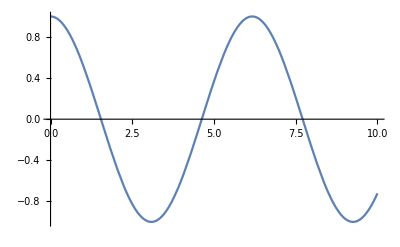

```mathematica
Plot[Evaluate[x[t]/.sols],{t,0,10}]
```

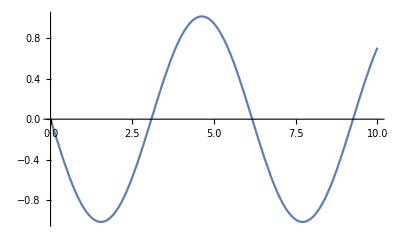

```mathematica
Plot[Evaluate[v[t]/.sols], {t, 0, 10}]
```

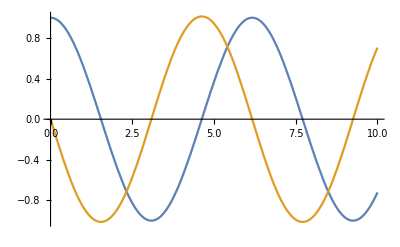

```mathematica
Plot[Evaluate[{x[t], v[t]}/.sols], {t,0, 10}]
```